120.

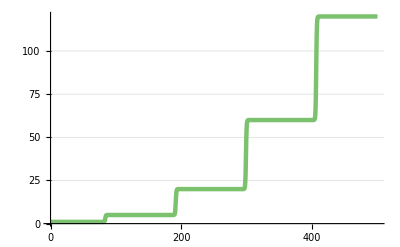

```mathematica
Get[NotebookDirectory[]<>"/factorial.m"]
rsys=Fact[5];
tmax=500;
sol=SimulateRxnsys[ExpandDiscreteRsys[rsys], tmax];
EvaluateRxnAtPoint[sol,f,tmax]
PlotForPaper[Evaluate[{f[t]}/.sol], tmax]
```